```mathematica
avogadroConstant=6.02214086*10^23;
oneOverGevToCm=0.197*10^-13;(*cm*)
cmToKm=10^-5;
evToGeV=10^-9;
values={
ne->2.2*avogadroConstant*oneOverGevToCm^3,(*GeV^3*)
gf->1.1663787*10^-5,(*GeV^-2*)
dm221->7.56*10^-5*evToGeV^2,(*GeV^2*)
dm231->2.55*10^-3*evToGeV^2,(*GeV^2*)
baseline->810*10^5/oneOverGevToCm,(*GeV^-1*)
theta13->8.41*Degree,
theta12->34.5*Degree
(*theta23->41.*Degree*)
(*delta->252.*Degree*)
};
```

```mathematica
getAppearanceProbability[e_,deltaCp_,isNu_,th23_,normalOrdering_]=Module[{sign,a,d21,d31,prob},
sign=If[isNu,1,-1];
(*a=sign*gf*ne/Sqrt[2]*10^-10;*)
a=sign*gf*ne/Sqrt[2];
(*a=sign/3500*oneOverGevToCm*cmToKm;(*GeV, NunokawaPV08*)*)
d21=dm221/(4*e)*baseline;
d31=dm231/(4*e)*baseline;

prob=Sin[theta23]^2*Sin[2*theta13]^2*Sin[d31-a*baseline]^2/(d31-a*baseline)^2*d31^2
+Cos[theta23]^2*Sin[2*theta12]^2*Sin[a*baseline]^2/(a*baseline)^2*d21^2
+Sin[2*theta23]*Sin[2*theta13]*Sin[2*theta12]*Sin[d31-a*baseline]/(d31-a*baseline)*d31*Sin[a*baseline]/(a*baseline)*d21*Cos[d31+delta];
prob/.values/.delta->deltaCp*sign/.theta23->th23
];
```

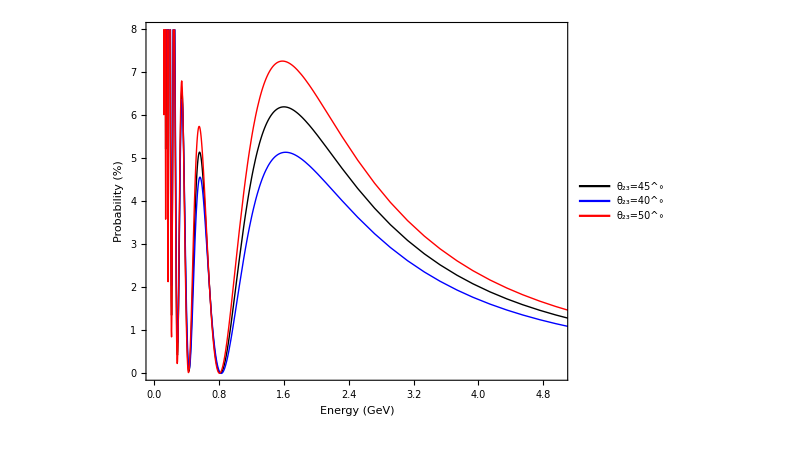

```mathematica
(*compare nue disappearance*)
plot=Plot[{
getAppearanceProbability[x,0,True,45.*Degree]*100,
getAppearanceProbability[x,0,True,40.*Degree]*100,
getAppearanceProbability[x,0,True,50.*Degree]*100
},
{x,0.1,10},
PlotLegends->Placed[LineLegend[{"θ_23=45^∘","θ_23=40^∘","θ_23=50^∘"},LegendMarkerSize->40],{0.75,0.75}],
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Red,Thick]},
PlotRange->{{0,5},{0,8}},
ImageSize->600,
AspectRatio->600/800,
BaseStyle->{FontSize->20},
Frame->True,
FrameLabel->{{"Probability (%)",None},{"Energy (GeV)",None}},
FrameStyle->Directive[Black,Thick]
]
(*Export["/Users/juntinghuang/Desktop/nova/oscillation/figures/nue.pdf",plot]*)
```

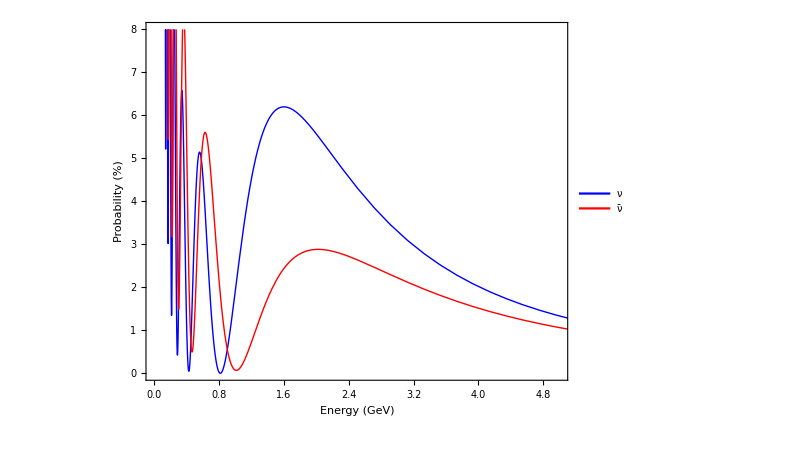

```mathematica
plot=Plot[{
getAppearanceProbability[x,0,True,45.*Degree]*100,
getAppearanceProbability[x,0,False,45.*Degree]*100
},
{x,0.1,10},
PlotLegends->Placed[LineLegend[{"ν","ν̄"},LegendMarkerSize->40],{0.75,0.75}],
PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},
PlotRange->{{0,5},{0,8}},
ImageSize->600,
AspectRatio->600/800,
BaseStyle->{FontSize->20},
Frame->True,
FrameLabel->{{"Probability (%)",None},{"Energy (GeV)",None}},
FrameStyle->Directive[Black,Thick]
]
```

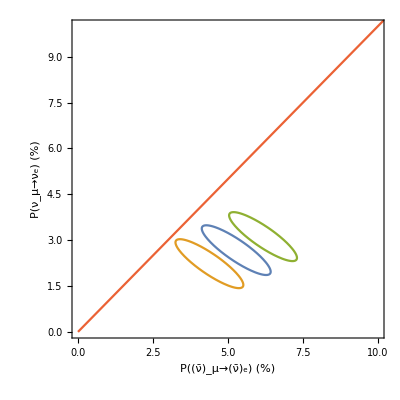

```mathematica
biprob=ParametricPlot[{
{getAppearanceProbability[2,x,True,45*Degree]*100,getAppearanceProbability[2,x,False,45*Degree]*100},
{getAppearanceProbability[2,x,True,40*Degree]*100,getAppearanceProbability[2,x,False,40*Degree]*100},
{getAppearanceProbability[2,x,True,50*Degree]*100,getAppearanceProbability[2,x,False,50*Degree]*100},
{x*2,x*2}
},
{x,0,2*Pi},
PlotRange->{{0,10},{0,10}},
ImageSize->400,
AspectRatio->1,
Frame->True,
FrameLabel->{{"P(ν_μ→ν_e) (%)",None},{"P((ν̄)_μ→(ν̄)_e) (%)",None}},
FrameStyle->Directive[Black,Thick],
BaseStyle->{FontSize->20}
]
```